# Polarization Under Low B - field and Hight T

```mathematica
(* set the absolute temperature and the convertion to Celsius *)
T0=-273.15;
CelsiusToK[x_]:=x-T0;
```

(* the thermal polarization is given by the Boltzmann statistic.The excited and the ground state population is: *)
Nup= N0 Exp[ -Εup/(kB T)]
Ndn= N0 Exp[ -Εdn/(kB T)]
(* we define the energy of the up-state is higher *) 
Eup = μ B
Edn = -μ B
(* thus, the ratio of the 2 population is *)
Nup/Ndn=Exp[-(Eup+Edn)/(kB T)]=Exp[-2(μ B)/(kB T)]
(* the thermal polarization is the ratio of the different of spin-up and spin-down to the total spin *)
Pthermal = (Nup-Ndn)/(Nup+Ndn)=- Tanh[(μ B)/(kB T)]
(* the minus sign means the polarization is opposite to the direction of the B-field *)

```mathematica
(* where μ is the proton magnetic moment. kB is the Boltzmann constant.*)
μ=1.41061*10^-26  J T^-1;
kB =1.3806504 *10^-23 J K^-1;
```

```mathematica
(* The proton magnetic moment is small,the thermal polarization can be approximated as a linear function:*)
Series[Tanh[x],{x,0,6}]
```

x-x^3/3+(2 x^5)/15+O[x]^7

```mathematica
(* since our polarization is on T = 268^0 C and B = 0.05 T ,thus,the thermal polarization is:*)
Pth[temp_,field_]:=Tanh[(μ field T)/(kB  temp K)]
Pth[300,0.3]
Pth[77,0.3]
```

1.0217×10^-6

3.98065×10^-6

```mathematica
Tanh[(ℏ γp 0.3)/(kB  300 K)kg/(C s)]
```

2.04339×10^-6

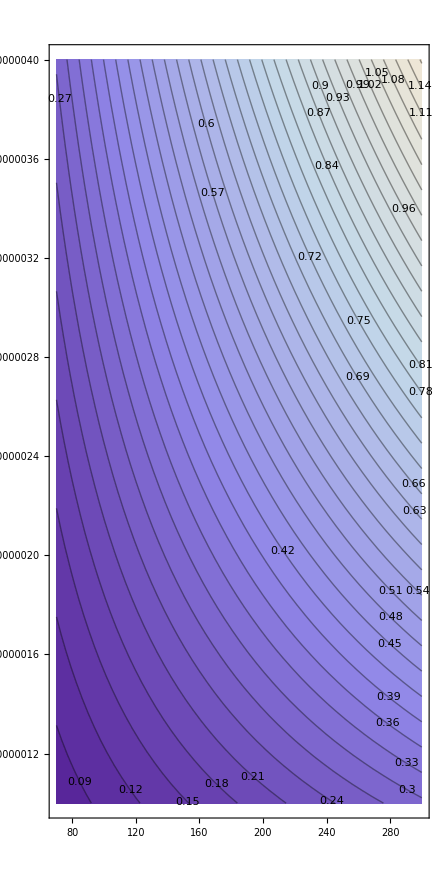

```mathematica
(* a contour plot of the Polarization aginst temperature, the contours are the B-field Strength *)
ContourPlot[((μ T)/(kB Temp K))^-1 ArcTanh[p],{Temp,70,300},{p,1 10^-6,4 10^-6},AspectRatio->2,Contours->Range[0.00,2,0.03],ContourLabels->True]
```